```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Morphological Operations

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Mathematical morphology is a kind of local processing where the transformations are based on logical (binary) operations. This means that the opeations can sometimes be interpreted as operating on the spatial structure of objects in a scene (the shape of pixel groupings) rather than on the amplitude values of the pixels. Like all local operators, binary morphological operators may be implemented using convolution-like algorithms. The fundamental operations of morphology replace the addition and multiplication of standard convolution with logical ORs and ANDs.

The ideas can be presented in several ways: as a set-theoretic method, as a set of logical (bitwise) operations on a binarized image, and in terms of a collection of algorithms that are intended to acccomplish certain image processing tasks. For example, the basic operations of erosion and dilation can be defined in terms of set operations, in terms of binary logical operations, and can also be extended in a sensible way to the processing of grayscale images.

### Morphological Operators

#### Set Description of Binary Images

Mathematical morphology can be described in terms of set theory. Sets in mathematical (image) morphology may represent the shapes which are visible in binary images. The set of all the white (or black) pixels in a binary image constitutes a complete description of the image. Each element of the set is a 2-vector of integer values identifying the coordinates of each white (or black) pixel with respect to some assumed coordinate center, which is typically the a upper-left element of the array.

A set description α of a binary image A is obtained by locating all the ones in the image. Here is a binary matrix and its set description.

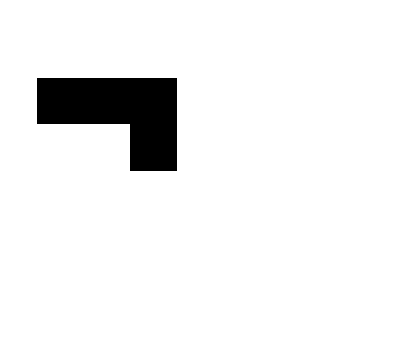
{(0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-,(1 | 0
1 | 1
1 | 2
2 | 2)}

```mathematica
a = {{0,0,0,0,0,0,0},{1,1,1,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}};
α = Position[a,1]-1 ;
{a //MatrixForm, ArrayPlot[a],α //MatrixForm}
```

Position[ ] extracts the coordinates of the elements from the matrix representation. It is also possible to go backwards by using the set representation as indices into a matrix. α is the set description and {r,c} defines the size of the binary matrix in which to embed the set.

```mathematica
setToMatrix[α_,{r_,c_}]:=Module[{},outMat = ConstantArray[0,{r,c}];Map[(outMat[[#[[1]],#[[2]]]]=1)&,α+1]; outMat]
```

There are three basic set operations: complement, translation, and reflection. The set complement, denoted by ᾱ, is given by the positions of the zero-valued elements. This is sometimes called the background image.

```mathematica
αBar = Position[a,0]-1
```

{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{1,3},{1,4},{1,5},{1,6},{2,0},{2,1},{2,3},{2,4},{2,5},{2,6},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6}}

The translation of a set α by a point (or vector) x, denoted α_x, is defined by

α_x = {a+x : a∈ α}

In Mathematica, it makes sense to define a function that translates a set a by x

```mathematica
setTranslate[a_,x_]:=Map[(x+#)&,a];
```

For example, the translation of α by {1,2} is

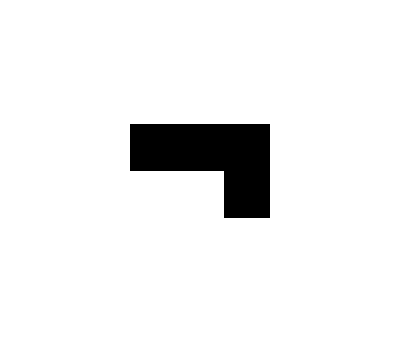
{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-,(2 | 2
2 | 3
2 | 4
3 | 4)}

```mathematica
αTrans = setTranslate[α,{1,2}];
aTrans = setToMatrix[αTrans,{6,7}];
{aTrans//MatrixForm,ArrayPlot[aTrans],αTrans//MatrixForm}
```

The reflection of a set α, denoted α^⋁, is defined

α^⋁ = {-a : a∈ α }

Reflecting the set α and then translating back (so that it lies in the same space as before)

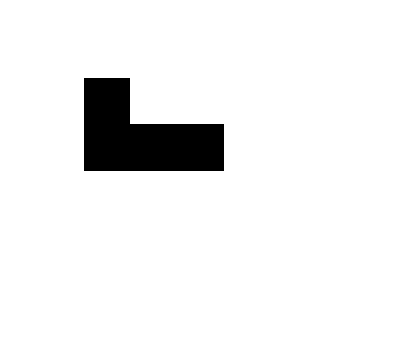
{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-,(2 | 3
2 | 2
2 | 1
1 | 1)}

```mathematica
αReflect = setTranslate[-α,{3,3}];
aReflect = setToMatrix[αReflect,{6,7}];
{aReflect//MatrixForm,ArrayPlot[aReflect],αReflect//MatrixForm}
```

#### Dilation

The set theoretic concepts of translation, set complementation, and reflection can be used to define dilation and erosion, the two of the fundamental operators of binary morphology. These operators can be represented either in the form of set descriptions or in a matrix formulation.

Dilation combines two sets using vector addition of the set elements. Formally, the binary dilation of set α by a set β (called the structuring element, which defines the neighborhood over which the local processing is done), denoted α ⊕ β, is the union of all translates of  α by all elements of β. For example,

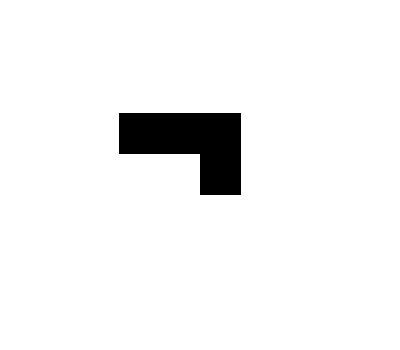
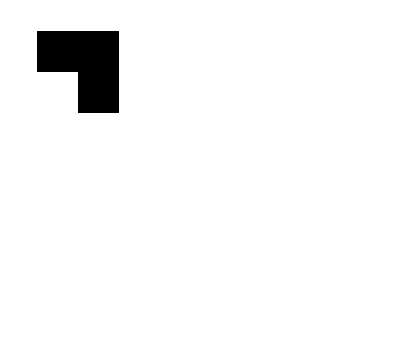
{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-,(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-}

```mathematica
α={{2,2},{2,3},{2,4},{3,4}}; αMat = setToMatrix[α,{7,8}];
β={{0,0},{0,1},{1,1}}; βMat = setToMatrix[β,{7,8}];
{αMat//MatrixForm, ArrayPlot[αMat],βMat//MatrixForm,ArrayPlot[βMat]}
```

Dilation takes the vector addition of the set elements, which can be accomplished using the generalized outer product Outer[ ]

```mathematica
Outer[Plus,β,α,1]
```

{{{2,2},{2,3},{2,4},{3,4}},{{2,3},{2,4},{2,5},{3,5}},{{3,3},{3,4},{3,5},{4,5}}}

There may be some duplicates, which can be removed using Union[ ] (Flatten[ ] is needed to get all the elements at the same level).

```mathematica
dilαβ = Union[Flatten[Outer[Plus,β,α,1],1]]
```

{{2,2},{2,3},{2,4},{2,5},{3,3},{3,4},{3,5},{4,5}}

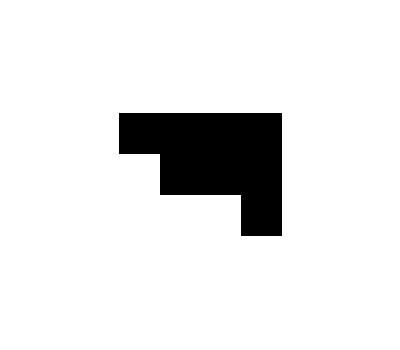
{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-,(2 | 2
2 | 3
2 | 4
2 | 5
3 | 3
3 | 4
3 | 5
4 | 5)}

```mathematica
dilαβMat = setToMatrix[dilαβ,{7,8}];{dilαβMat//MatrixForm, ArrayPlot[dilαβMat],dilαβ//MatrixForm}
```

Equivalently, this is equal to the set of all positions of the reflected set β^⋁ for which it intersects with, or "hits", set α.

α⊕β = ∪_(x ϵ β)α_x = {x : (β^⋁)_x∩α ≠0}

Dilation is commutative and associative. It also distributes over the union of two structuring elements: α⊕(β∪γ)=(α⊕β)∪(α⊕γ). Dilation is also an increasing operation, namely, for any two sets α_1  and α_2 such that α_1⊂α_2 (where ⊂ means "is contained in") then α_1⊕β ⊂ α_2⊕β.  Also given two structuring elements such that, β_1⊂ β_2,  α ⊕β_1 ⊂  α ⊕β_2.  Finally, dilation is also translation invariant, α⊕β_x=(α⊕β)_x, namely dilating with a translated structuring element is equivalent to translating the result.

Probably the easiest way to think of dilation is as the union of all the translates b+α where of b ranges over all elements of β. For the above example, β has three elements

```mathematica
β
```

{{0,0},{0,1},{1,1}}

The three translates of α are:

```mathematica
αTrans1 = setTranslate[α,β[[1]]]; αMat1= setToMatrix[αTrans1,{6,7}];
αTrans2 = setTranslate[α,β[[2]]]; αMat2= setToMatrix[αTrans2,{6,7}];
αTrans3 = setTranslate[α,β[[3]]]; αMat3= setToMatrix[αTrans3,{6,7}];
Map[MatrixForm,{αMat1,αMat2,αMat3}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
{setToMatrix[{{2,2},{2,3},{2,4},{3,4}},{6,7}],setToMatrix[{{2,3},{2,4},{2,5},{3,5}},{6,7}],setToMatrix[{{3,3},{3,4},{3,5},{4,5}},{6,7}]}
```

{{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,1,1,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,1,1,1,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,1,1,1,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,0}}}

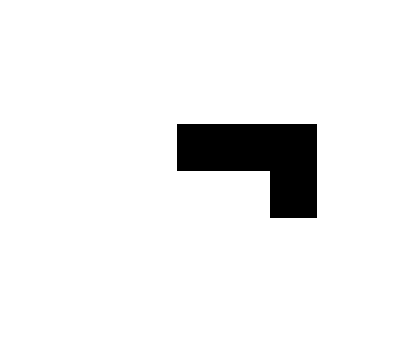
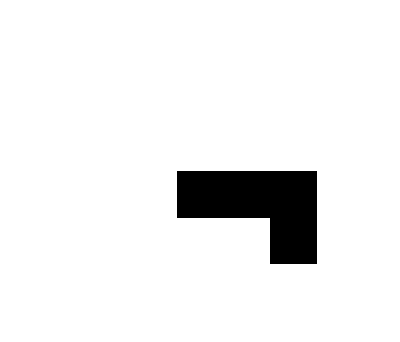
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ArrayPlot,{αMat1,αMat2,αMat3}]
```

```mathematica
{ArrayPlot[setToMatrix[{{2,2},{2,3},{2,4},{3,4}},{6,7}]],ArrayPlot[setToMatrix[{{2,3},{2,4},{2,5},{3,5}},{6,7}]],ArrayPlot[setToMatrix[{{3,3},{3,4},{3,5},{4,5}},{6,7}]]}
```

{-Graphics-,-Graphics-,-Graphics-}

The union of these three translates is:

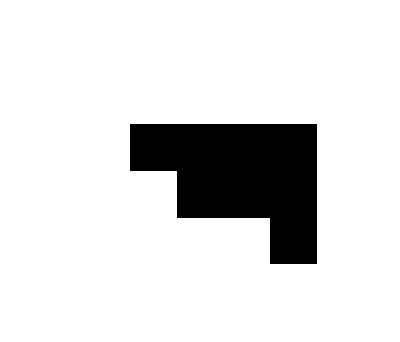
{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-}

```mathematica
{Sign[αMat1+αMat2+αMat3]//MatrixForm,ArrayPlot[Sign[αMat1+αMat2+αMat3]]}
```

#### Erosion

Erosion is the morphological "dual" of dilation. The erosion of set α by a set β, denoted α ⊖ β, is the set intersection of all negative translates of set α by elements of set β. Equivalently, erosion is the set of all positions for which set β is a subset of α (i.e., it "fits" inside α).

α⊖β = ∩_(x ϵ β)α_-x = {x : β_x⊂ α}

Erosion is neither commutative or associative. A modified associative property of erosion is as follows: (α⊖β) ⊖γ = α⊖(β ⊕γ ), where β and γ are two structuring elements. Distribution over the union of two structuring elements takes the following form: 

α⊖(β ∪ γ) = (α ⊖ β)  ∩ (α ⊖ γ). 

Like dilation, erosion is increasing with respect to set α, but is decreasing with respect to the structuring element, namely, if β_1⊂β_2 (where ⊂ means "is contained in") then α⊖β_1 ⊃ α⊖β_2.

This gives the result of eroding α by β. First, Outer[ ] calculates the negative translates of α.

```mathematica
Outer[Plus,-β,α,1]
```

{{{2,2},{2,3},{2,4},{3,4}},{{2,1},{2,2},{2,3},{3,3}},{{1,1},{1,2},{1,3},{2,3}}}

and the intersection gives the desired result.

```mathematica
Apply[Intersection,Outer[Plus,-β,α,1]]
```

{{2,3}}

The three translates of α are:

```mathematica
αTrans1 = setTranslate[α,-β[[1]]]; αMat1= setToMatrix[αTrans1,{6,7}];
αTrans2 = setTranslate[α,-β[[2]]]; αMat2= setToMatrix[αTrans2,{6,7}];
αTrans3 = setTranslate[α,-β[[3]]]; αMat3= setToMatrix[αTrans3,{6,7}];
Map[MatrixForm,{αMat1,αMat2,αMat3}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

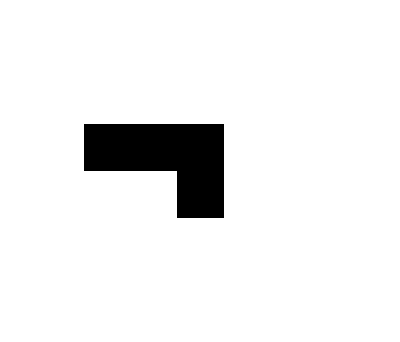
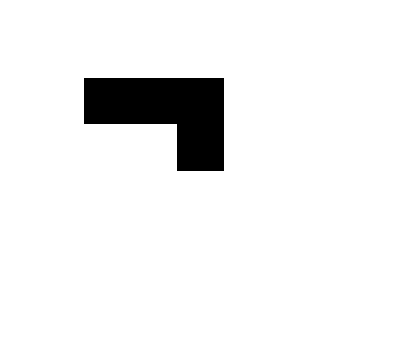
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[αMat1],ArrayPlot[αMat2],ArrayPlot[αMat3]}
```

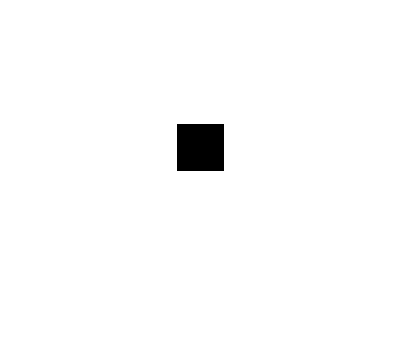
{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-}

```mathematica
αIntersection = αMat1 αMat2 αMat3;
{αIntersection//MatrixForm,ArrayPlot[αIntersection]}
```

Dilation and erosion are duals of each other, that is, they can be defined in terms of each other. The duality relationships are:

OverBar[α⊖β]= ᾱ ⊕ β^⋁

OverBar[α⊕β]= ᾱ ⊖ β^⋁

#### Convolutional formulas for Dilation and Erosion

For purposes of signal and image processing it is preferable to consider formulations of erosion and dilation in terms of arrays instead of sets - this leads to realizations of the operators that are strikingly similar to convolution and correlation. Recall that linear convolution of a one-dimensional (1D) signal f with filter h is defined (𝒟_h denotes the region of support of filter h).

(f*h)(x) = ∑_(i ∈𝒟_h)^ f(x-i) h(i)

The dilation of a signal f with structuring element s may likewise be written in a convolution-like form (𝒟_s denotes the region of support of structuring element s).

(f⊕ s)(x) =∨_(i∈𝒟_s)f(x-i) ∧s(i)

where symbols ∨ and ∧ are the logical OR and logical AND operators, respectively. Therefore dilation is also a scanning process with the algebraic multiplication and addition operators replaced by Boolean and and or, respectively. Thus the structuring element plays an analogous role in morphological signal processing to the FIR filter in LSI signal processing.  In the 2D case, with a binary signal f and structuring element s of dimensions 2n+1×2n+1

(f⊕ s)(x, y) = ∨_(i=-n)^n∨_(j=-n)^n s(i, j) ∧ f(x-i,y-j)

Assuming the common case of a uniform, square structuring element of dimensions 3×3, dilation takes the form.

(f⊕ s)(x, y) = f(x+1,y+1) ∨f(x+1,y) ∨ f(x+1,y-1) ∨ f(x,y+1) ∨ f(x,y) ∨ f(x,y-1) ∨ f(x-1,y+1) ∨ f(x-1, y) ∨ f(x-1,y-1)

This shows that the result at a point (x,y) is equal to 1 as long as at least one non-zero pixel is encountered in its local neighborhood. This can be implemented using the general form of ListConvolve[ ], where the function g[ ] (in this case BitAnd) is used in place of Times and where the function h[ ] (in this case BitOr) is used in place of Plus.

```mathematica
?ListConvolve
```

RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"]}], "]"}] forms the convolution of the kernel StyleBox["ker", "TI"] with StyleBox["list", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["k", "TI"]}], "]"}] forms the cyclic convolution in which the StyleBox["k", "TI"]SuperscriptBox["", "th"] element of StyleBox["ker", "TI"] is aligned with each element in StyleBox["list", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}]}], "]"}] forms the cyclic convolution whose first element contains RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", "1", "]"}], "]"}], RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], "]"}], "]"}]}] and whose last element contains RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", RowBox[{"-", "1"}], "]"}], "]"}], RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]], "]"}], "]"}]}]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["p", "TI"]}], "]"}] forms the convolution in which StyleBox["list", "TI"] is padded at each end with repetitions of the element StyleBox["p", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] forms the convolution in which StyleBox["list", "TI"] is padded at each end with cyclic repetitions of the SubscriptBox[StyleBox["p", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"]}], "]"}] forms a generalized convolution in which StyleBox["g", "TI"] is used in place of Times and StyleBox["h", "TI"] in place of Plus. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"], ",", StyleBox["lev", "TI"]}], "]"}] forms a convolution using elements at level StyleBox["lev", "TI"] in StyleBox["ker", "TI"] and StyleBox["list", "TI"].

Assuming an odd-sized structuring element with the origin centered in the array, define a 3×3 array B corresponding to set β={{0,0},{0,1},{1,1}} as follows:

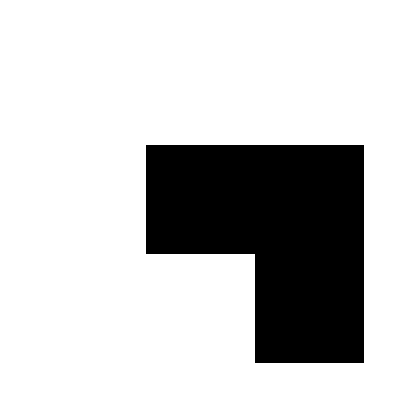

```mathematica
B = {{0,0,0},{0,1,1},{0,0,1}};
GraphicsRow[{MatrixForm[B],ArrayPlot[B]},ImageSize->Small]
```

The matrix A corresponding to set α is

```mathematica
A = setToMatrix[α,{6,7}];
{MatrixForm[A],ArrayPlot[A]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-}

The binary dilation of image A by structuring element B, namely A⊕B, is given by

```mathematica
dilAB = ListConvolve[B,A,2,0,BitAnd,BitOr];
{dilAB//MatrixForm, ArrayPlot[dilAB]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-}

As in the case of dilation, erosion may also be defined as a convolution over a Boolean algebra. Using the duality property and DeMorgan's theorem gives

(f⊖ s)(x) | = | (OverBar[f̄⊕s^⋁])(x)
  | = | OverBar[∨_(i ∈𝒟_s)f̄(x-i) ∧s(-i)] 
  | = | ∧_(i ∈𝒟_s)OverBar[f̄(x-i) ∧s(-i)]
  | = | ∧_(i ∈𝒟_s)f(x-i) ∨s^—(-i)
  | = | ∧_(i ∈𝒟_s)f(x+i) ∨s^—(i)

where 𝒟_s denotes the region of support of structuring element s. In the 2D case, with a binary signal f and structuring element s of dimensions 2n+1×2n+1,

(f⊖ s)(x, y) = ∧_(i=-n)^n∧_(j=-n)^n s^—(i, j) ∨ f(x+i,y+j)

For the special case of a uniform, square structuring element of dimensions 3×3

(f⊖ s)(x, y) = f(x-1,y-1)∧f(x-1,y)∧f(x-1,y+1)∧f(x,y-1)∧f(x,y)∧f(x,y+1)∧f(x+1,y-1)∧f(x+1,y)∧f(x+1,y+1)

Thus erosion is a "product" (Boolean AND) of all the pixels in the local neighborhood. Because the structuring element is reflected, the equivalent erosion formula uses ListCorrelatie[] instead of ListConvolve[ ], and the binary erosion of array A by structuring element B, A ⊖ B is

```mathematica
erodeAB = ListCorrelate[1-B,A,2,1,BitOr,BitAnd];
{erodeAB//MatrixForm, ArrayPlot[erodeAB]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),-Graphics-}

The operations of binary erosion and dilation can be applied even more easily to images using the Dilation[] and Erosion[ ] functions.

```mathematica
bw=-Graphics-;
```

```mathematica
bw=-Graphics-;
```

#### Closing and Opening

Dilation and erosion are often applied to an image in concatenation. Dilation followed by erosion is called a close operation.

A • B = ( A ⊕ B ) ⊖ B

The closing of an image with a compact structuring element without holes smooths the contours of objects and eliminates holes in objects. The closing operation satisfies the following properties:

(i) Closing is extensive, i.e., A is a subset (subimage) of A • B

(ii) Closing is idempotent, i.e., (A • B) • B = A • B

The importance of idempotence is that once an image has been closed, subsequent closings produce no further effects. Most operators continue to change an image as they are applied iteratively. The binary closure operator can be written explicitly in terms of erosion and dilation.

```mathematica
dilateAB = ListConvolve[B,A,2,0,BitAnd,BitOr];
closeAB = ListCorrelate[1-B,dilateAB,2,1,BitOr,BitAnd];
Map[MatrixForm,{A,dilateAB, closeAB}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

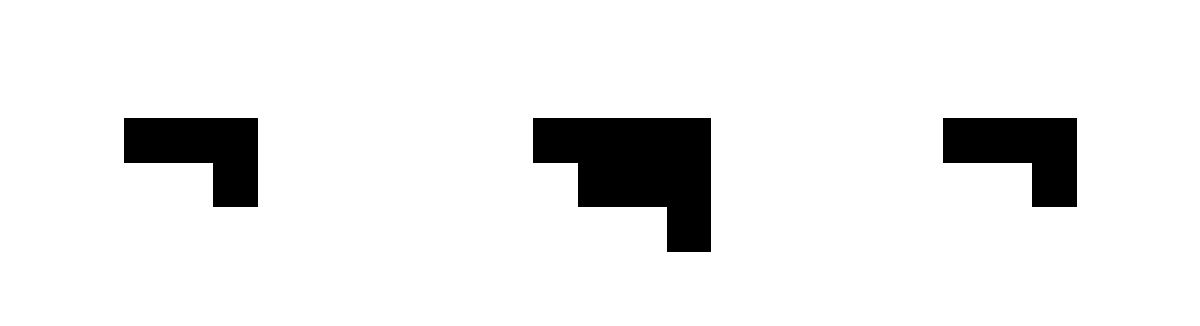

```mathematica
GraphicsRow[Map[ArrayPlot,{A,dilateAB,closeAB}]]
```

Or, more simply

```mathematica
GraphicsRow[{Erosion[Dilation[Image[A],B],B],Closing[Image[A],B]}]
```

-Graphics-

Open, which is the morphological dual of close, consists of erosion followed by dilation.

A ◦ B = (A ⊖ B ) ⊕ B

Objects that are removed by the structuring element in the erosion step are never recovered, therefore object structures may be selectively filtered out depending on the chosen size and shape of the filter. The opening operation satisfies the following properties:

(i) Opening is antiextensive, i.e., A ◦ B is a subset (subimage) of A

(ii) Opening is idempotent, i.e., (A ◦ B) ◦ B = A ◦ B

This shows an implementation of the binary open operation.

```mathematica
erodeAB = ListCorrelate[1-B,A,2,1,BitOr,BitAnd];
openAB =ListConvolve[B,erodeAB,2,0,BitAnd,BitOr];
Map[MatrixForm,{A,erodAB,openAB}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

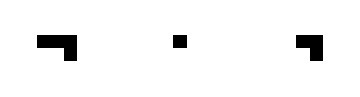

```mathematica
GraphicsRow[Map[ArrayPlot,{A,erodeAB,openAB}],ImageSize->Medium]
```

Or, more simply

```mathematica
GraphicsRow[{Dilation[Erosion[Image[A],B],B],Opening[Image[A],B]}]
```

-Graphics-

Opening of an image smooths the contours of objects, eliminates small objects, and breaks narrow strokes. Open and close satisfy the following duality relationships:

OverBar[A • B] = Ā ◦ B^⋁

OverBar[A ◦ B] = Ā • B^⋁

where the symbol Ā represents a binary complement of the elements of a binary array A and B^⋁ denotes the reflection of B. Here we prove the duality property in (13) using the duality relationships for erosion and dilation in Equations (3) and (4).

OverBar[A • B]= OverBar[( A ⊕ B ) ⊖ B] = OverBar[( A ⊕ B )]⊕ B^⋁= (Ā ⊖ B^⋁ )⊕ B^⋁= Ā ◦ B^⋁

Problem 9.3.4. Prove the identity in Equation (14) and computationally verify the duality relationships using matrices A and B.

In the following evaluation, I demonstrate the effect of close and open operations on the binary example image using structuring elements of increasing dimensions. Note how closing fills-in objects and smooths borders while opening removes small structures (original image shown in the center).

### Grayscale Morphological Operators

#### Dilation and Erosion

The definitions of binary morphology extend naturally to the domain of digital grayscale signals with translation and reflection defined as before while Boolean AND and OR become point-wise minimum and maximum operators, respectively. Therefore grayscale dilation and erosion may also be implemented as convolution-like operators. In the general case of a non-flat structuring element and assuming 1D signals, dilation and erosion are defined by

(f⊕s)(x) = max _(y ϵ 𝒟_s) (f(x-y) + s(y) ) ,

(f⊖s)(x) = min _(y ϵ 𝒟_s) (f(x+y) - s(y) )

Assuming the structuring element is constant within 𝒟_s, grayscale dilation and erosion are

(f⊕s)(x) = max _(y ϵ 𝒟_s) f(x-y) ,

(f⊖s)(x) = min _(y ϵ 𝒟_s) f(x+y) .

For example, with a 3×3 uniform structuring array, dilation and erosion are

(f⊕s)(x,y) = max ( f(x+1,y+1), f(x+1,y), f(x+1,y-1), f(x,y+1), f(x,y), f(x,y-1), f(x-1,y+1), f(x-1,y-1), f(x-1,y-1) ).

(f⊖s)(x,y) = min ( f(x+1,y+1), f(x+1,y), f(x+1,y-1), f(x,y+1), f(x,y), f(x,y-1), f(x-1,y+1), f(x-1,y-1), f(x-1,y-1) ).

Dilation (max) tends to grow the white regions of an image. If the structuring element has positive values, the resulting image tends to become brighter. Erosion (min) decreases the white regions. With a 3×3 structuring element of zeros applied to the box-like image on the left, the dilation is shown in the middle and the erosion on the right.

```mathematica
A=PadRight[{{1,1,1},{1,3,3},{1,2,1},{1,1,1}},{8,8},0,2];
B={{0,0,0},{0,0,0},{0,0,0}};
dilAB = ListConvolve[B,A,2,-∞,Plus,Max];
erodAB = ListCorrelate[-B,A,2,∞,Plus,Min];
Map[MatrixForm,{A,dilAB,erodAB}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 3 | 3 | 0 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 3 | 3 | 3 | 3 | 0 | 0
0 | 1 | 3 | 3 | 3 | 3 | 0 | 0
0 | 1 | 3 | 3 | 3 | 3 | 0 | 0
0 | 1 | 2 | 2 | 2 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

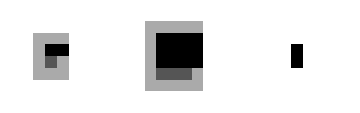

```mathematica
GraphicsRow[Map[ArrayPlot,{A,dilAB,erodAB}],ImageSize->Medium]
```

#### Morphological Reconstruction

Reconstruction from markers is an important category of morphological operators as many image processing tasks have a natural formulation in terms of these operators. Unlike the fundamental operators presented thus far which take as inputs an image and a structuring element, reconstruction requires two input images. During reconstruction some fundamental operator (for example, dilation or erosion) is applied repeatedly to the marker image, while the result of each operation is constrained by the second images called the mask. This section presents an example of reconstruction by geodesic dilation for binary images. A sequence of n conditional dilations is known as a size-n geodesic dilation where a conditional dilation is defined as the intersection of the mask image g with a dilation of the marker image f.

(f ⊕_g s) = (f ⊕ s) ∧ g

Reconstruction of image g from the marker image f is accomplished by repeating the conditional dilations until the result no longer changes.

R_g^⊕(f) = (f ⊕_g s)^n = (((f ⊕_g s) ⊕_g s) ... ⊕_g s)

where n is such that (f ⊕_g s)^n = (f ⊕_g s)^(n+1).

Here is a marker image f =(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) and a mask image g=(0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1).

Three consecutive conditional dilations of the marker image with a flat structuring element of dimensions 3×3, at which point further conditional dilations do not change the result.

(f ⊕_g s)^1 =  (0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0), (f ⊕_g s)^2 = (0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0), (f ⊕_g s)^3 = (0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0).

The Mathematica implementation of reconstruction by geodesic dilation is straightforward. Here are two image arrays.

```mathematica
A={{0,0,1,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}};
B={{0,1,1,0,0},{0,1,1,0,0},{1,1,1,0,1},{0,1,0,0,1},{0,0,0,1,1}};
```

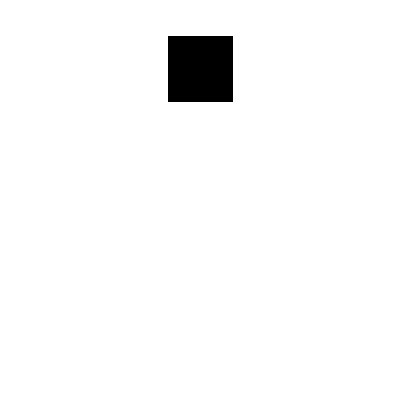
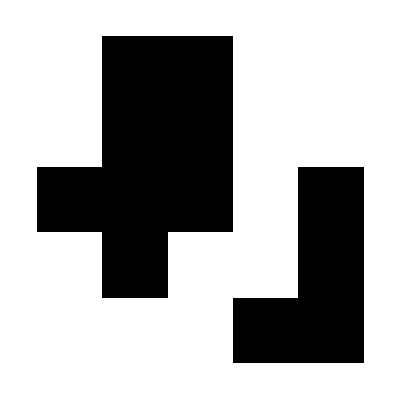

```mathematica
{ArrayPlot[A],ArrayPlot[B]}
```

The reconstruction of B from marker image A can be computed

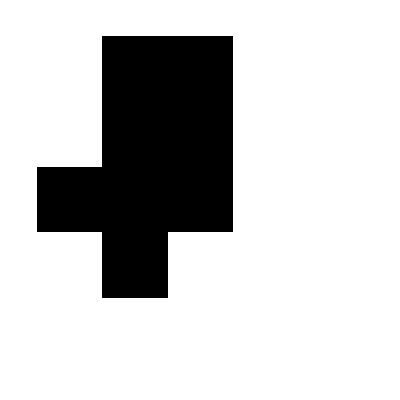
{(0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),-Graphics-}

```mathematica
fixedP = FixedPoint[B ImageData[Dilation[Image[#],1],"Bit"]&,A];
{MatrixForm[fixedP],ArrayPlot[fixedP]}
```

Or use the built in function GeodesicDilation[ ].

```mathematica
Image[GeodesicDilation[Image[A],Image[B]],ImageSize->Small]
```

-Graphics-

A conditional erosion is the union of the mask image g with an erosion of the marker image f. A sequence of n conditional erosions is called the size-n geodesic erosion.

(f ⊖_g s) = (f ⊖ s) ∨ g

Reconstruction of the image g from the marker image f can be accomplished by repeating the conditional erosions until the result no longer changes.

R_g^⊖(f) = (f ⊖_g s)^n = (((f ⊖_g s) ⊖_g s) ... ⊖_g s)

where n is such that (f ⊖_g s)^n = (f ⊖_g s)^(n+1).

For example, here is a marker image f =(1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1) and a mask image g=(1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0).

Three consecutive conditional erosions of the marker image with a flat structuring element of dimensions 3×3, at which point further conditional dilations do not change the result. The conditional erosions continue until the hole in the mask image is filled.

(f ⊖_g s)^1 =  (1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1), (f ⊖_g s)^2 = (1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0), (f ⊖_g s)^3 = (1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0).

The following shows the reconstruction of the mask image B from marker image A.

(1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

Clearly, evaluating the reconstruction could be time-consuming as the number of iterations is image dependent. Fortunately, efficient algorithms requiring a limited number of scans of the marker image are known. Here is an example of region filling using reconstruction by geodesic dilation.

```mathematica
{cells=-Graphics-,mask=Binarize[cells,0.69],{w,h}=ImageDimensions[cells]};
```

This defines a marker image, an all-zero image with a 1-valued seed placed anywhere within the background region of the original image. This seed defines the starting location of a flooding process that fills the background region.

```mathematica
mark=ConstantArray[0,{h,w}];
mark⟦153,83⟧=1;
filled=GeodesicDilation[Image[mark],mask];
```

```mathematica
{cells,mask,filled}
```

{-Graphics-,-Graphics-,-Graphics-}

#### Some Other Morphological Operators

There are some other morphological functions that are easy to find

```mathematica
?Morph*
```

```mathematica
?MorphologicalEulerNumber
```

RowBox[{"MorphologicalEulerNumber", "[", StyleBox["image", "TI"], "]"}] computes the morphological Euler number of regions in a binary image.
RowBox[{"MorphologicalEulerNumber", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["t", "TI"]}], "]"}] treats values above StyleBox["t", "TI"] as foreground.

Morphological Euler number counts the number of white objects minus the number of holes

```mathematica
im =; MorphologicalEulerNumber[im]
```

2

```mathematica
?MorphologicalComponents
```

RowBox[{"MorphologicalComponents", "[", StyleBox["image", "TI"], "]"}] gives an array in which each pixel of StyleBox["image", "TI"] is replaced by an integer index representing the connected foreground image component in which the pixel lies.
RowBox[{"MorphologicalComponents", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["t", "TI"]}], "]"}] treats values above StyleBox["t", "TI"] as foreground.

Find the connected components in a binary image

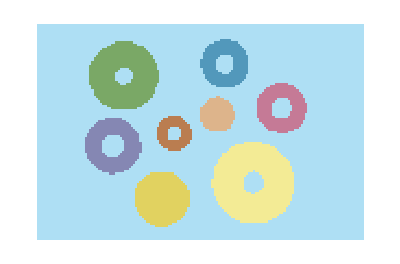

```mathematica
ArrayPlot[MorphologicalComponents[im],ColorFunction->"DarkBands"]
```

Count how many pixels are in each component:

```mathematica
Tally[Flatten[MorphologicalComponents[im]]]
```

{{0,11086},{1,327},{2,739},{3,348},{4,201},{5,171},{6,433},{7,1043},{8,502}}

```mathematica
?HitMissTransform
```

RowBox[{"HitMissTransform", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["ker", "TI"]}], "]"}] gives the hit-and-miss transform of StyleBox["image", "TI"] with respect to the composite structuring element StyleBox["ker", "TI"].
RowBox[{"HitMissTransform", "[", RowBox[{StyleBox["image", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["ker", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["ker", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives the union of the hit-and-miss transforms for all the structuring elements SubscriptBox[StyleBox["ker", "TI"], StyleBox["i", "TI"]].
RowBox[{"HitMissTransform", "[", RowBox[{StyleBox["image", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["ker", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["ker", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["t", "TI"]}], "]"}] treats values above StyleBox["t", "TI"] as foreground.

Hit-or-miss transform is an operation that detects a given configuration (or pattern) in a binary image, using the morphological erosion operator and a pair of disjoint structuring elements. The result of the hit-or-miss transform is the set of positions, where the first structuring element fits in the foreground of the input image, and the second structuring element misses it completely. Here's an example of finding all foreground pixels (1) that are immediately below a background pixel (0).

```mathematica
HitMissTransform[-Graphics-,{{-1},{1}}]
```

-Graphics-

Let C and D be two disjoint structuring elements. The pair (C, D) is sometimes called a "composite structuring element." The hit-or- miss transform of a given image A by the composite structuring element (C, D) is given by

-Graphics-

where A+c is the set complement of A. Thus a point x is in the hit- or-miss transform output if C translated to x lies inside A, and D translated to x misses A (fits the background of A).

```mathematica
Manipulate[If[rd==1,setToOne=Round[Abs[RandomVariate[NormalDistribution[100/2,100/4],{8,2}]]];
bwImg=RangeFilter[Dilation[Graphics[{White,Point[setToOne]},Background->Black],DiskMatrix[60]],10];rd=0;];
GraphicsRow[{bwImg,MorphologicalPerimeter[bwImg],Colorize[MorphologicalComponents[bwImg]]},ImageSize->800],{{rd,1,""},Button["New Image",rd=1]&},FrameLabel->Style["A binary image (left), it's perimeter (center), and a coloring of each connected component (right)",Medium],TrackedSymbols->{rd},SaveDefinitions->True]
```